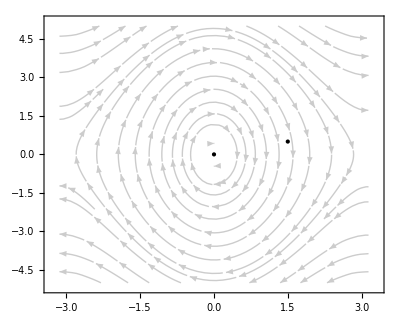

```mathematica
P1=StreamPlot[{y,-9/1.45 Sin[x]},{x,-Pi,Pi},{y,-5,5},AspectRatio->0.8,Epilog->{PointSize->Large,Point[{{0,0},{1.5,0.5}}]},StreamStyle->GrayLevel[0.8],StreamPoints->Medium,StreamScale->{0.15,50,0.01}]
```

```mathematica
s=NDSolve[{x'[t]==y[t],y'[t]==-9/1.45 Sin[x[t]],{x[0]==1.5,y[0]==0.5}},{x,y},{t,20}];
explicitEuler=Import["/home/khaled/Desktop/FileName.csv","CSV"];
P3=ListLinePlot[explicitEuler,PlotStyle->Blue];
implicitEuler=Import["/home/khaled/Desktop/FileName2.csv","CSV"];
P4=ListLinePlot[implicitEuler,PlotStyle->Blue];


symplecticEuler=Import["/home/khaled/Desktop/FileName3.csv","CSV"];
P5=ListLinePlot[symplecticEuler,PlotStyle->Blue];
```

```mathematica
ResourceFunction["MaTeXInstall"][]
Needs["MaTeX`"]
```

Paclet[MaTeX,1.7.9,<>]

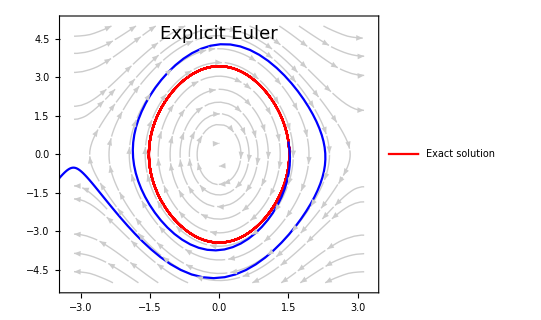

```mathematica
P2=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,20},PlotStyle->Red,PlotLegends->Placed[{"Exact solution"},{Left,Bottom}]];
Show[P1,P2,P3,FrameLabel->MaTeX@{"\\theta","\\dot \\theta"},LabelStyle->Black,PlotRangePadding->0,Epilog->{Text[Style["Explicit Euler",18],{0,4.7}]}]
```

```mathematica
ListLinePlot[explicitEuler,PlotMarkers->{"●", "■", "◆", "▲", "▼", "○", "□", "◇", Scaled[0.04]}]
```

-Graphics-

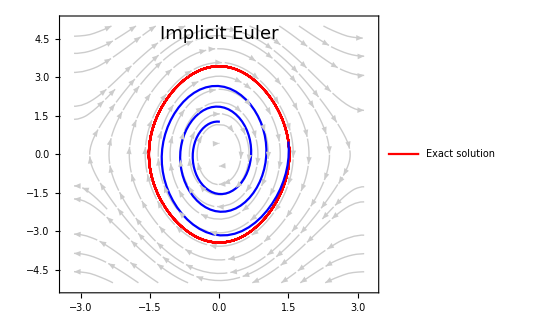

```mathematica
Show[P1,P2,P4,FrameLabel->MaTeX@{"\\theta","\\dot \\theta"},LabelStyle->Black,PlotRangePadding->0,Epilog->{Text[Style["Implicit Euler",18],{0,4.7}]}]
```

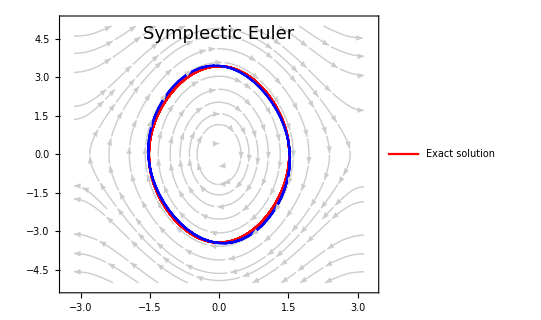

```mathematica
Show[P1,P2,P5,FrameLabel->MaTeX@{"\\theta","\\dot \\theta"},LabelStyle->Black,PlotRangePadding->0,Epilog->{Text[Style["Symplectic Euler",18],{0,4.7}]}]
```

```mathematica
Ham0=Import["/home/khaled/Desktop/H0.csv","CSV"];
H0=ListLinePlot[Ham0,PlotStyle->Red,PlotLegends->Placed[{"Exact energy"},{Left,Top}]];
Ham1=Import["/home/khaled/Desktop/H1.csv","CSV"];
H1=ListLinePlot[Ham1,PlotStyle->Darker[Green]];
Ham2=Import["/home/khaled/Desktop/H2.csv","CSV"];
H2=ListLinePlot[Ham2,PlotStyle->Gray];
Ham3=Import["/home/khaled/Desktop/H3.csv","CSV"];
H3=ListLinePlot[Ham3,PlotStyle->Blue];
```

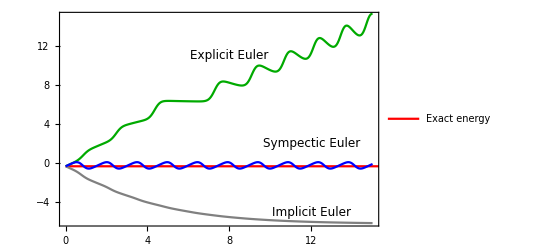

```mathematica
Show[H0,H1,H2,H3,FrameLabel->MaTeX@{"t",Energy},PlotRange->{{0,15},{-6,15}},Frame-> True,Axes->False,Epilog->{Text[Style["Sympectic Euler",12],{12,2}],Text[Style["Explicit Euler",12],{8,11}],Text[Style["Implicit Euler",12],{12,-5}]}]
```

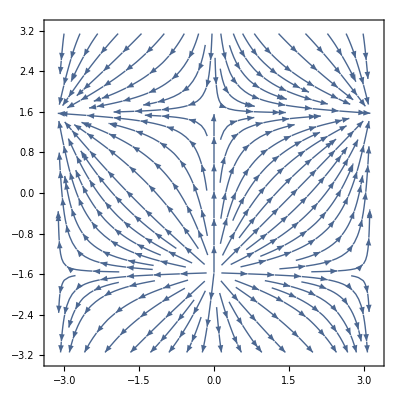

```mathematica
StreamPlot[{Sin[x],Cos[y]},{x,-Pi,Pi},{y,-Pi,Pi},StreamScale->{Automatic,Automatic,0.01}]
```

```mathematica
Q1=StreamPlot[{y,-0.2 y - x},{x,-1.5,1.5},{y,-1.5,1.5},AspectRatio->0.8,Epilog->{PointSize->Large,Point[{{0,0},{0,1.2}}]},StreamStyle->GrayLevel[0.8],StreamPoints->Medium,StreamScale->{0.15,50,0.01}];

s=NDSolve[{x'[t]==y[t],y'[t]==-0.2y[t]-x[t],{x[0]==0,y[0]==1.2}},{x,y},{t,16}];
Q2=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,16},PlotStyle->{Thickness[0.008],Red},PlotLegends->Placed[{"Exact solution"},{Left,Bottom}]];

phaseEXP=Import["/home/khaled/Desktop/phase-exp-h01.csv","CSV"];
Q3=ListLinePlot[phaseEXP,PlotStyle->Blue];

phaseIMP=Import["/home/khaled/Desktop/phase-imp-h01.csv","CSV"];
Q4=ListLinePlot[phaseIMP,PlotStyle->Blue];

phaseSYM=Import["/home/khaled/Desktop/phase-sym-h01.csv","CSV"];
Q5=ListLinePlot[phaseSYM,PlotStyle->Blue];


ResourceFunction["MaTeXInstall"][]
Needs["MaTeX`"]
```

Paclet[MaTeX,1.7.9,<>]

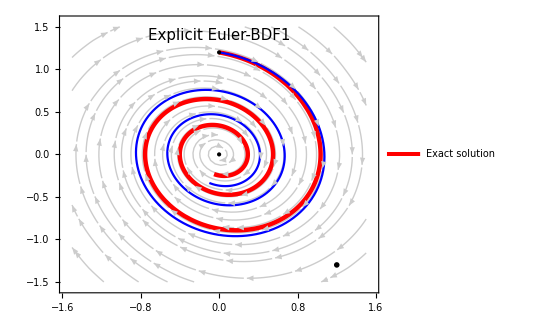

```mathematica
Show[Q1,Q2,Q3,FrameLabel->MaTeX@{"x","p"},LabelStyle->Black,PlotRangePadding->0,Epilog->{PointSize->Large,Point[{{0,0},{0,1.2}}],Text[MaTeX["h=0.05",FontSize->15],{1.2,-1.3}],Text[Style["Explicit Euler-BDF1",15],{0,1.4}]}]
```

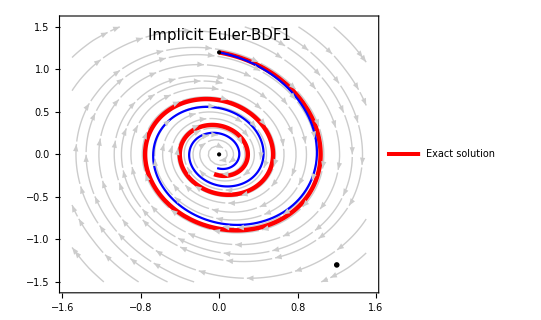

```mathematica
Show[Q1,Q2,Q4,FrameLabel->MaTeX@{"x","p"},LabelStyle->Black,PlotRangePadding->0,Epilog->{PointSize->Large,Point[{{0,0},{0,1.2}}],Text[MaTeX["h=0.05",FontSize->15],{1.2,-1.3}],Text[Style["Implicit Euler-BDF1",15],{0,1.4}]}]
```

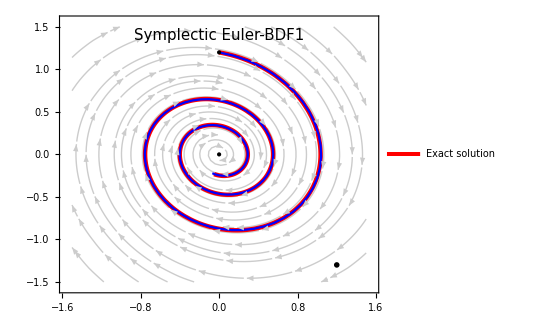

```mathematica
Show[Q1,Q2,Q5,FrameLabel->MaTeX@{"x","p"},LabelStyle->Black,PlotRangePadding->0,Epilog->{PointSize->Large,Point[{{0,0},{0,1.2}}],Text[MaTeX["h=0.125",FontSize->15],{1.2,-1.3}],Text[Style["Symplectic Euler-BDF1",15],{0,1.4}]}]
```